# Data PreProcessing

In this step data was extracted from the source “https://datarepository.wolframcloud.com/resources/United%2BStates%2Btornadoes%2B1950-2015”.
It consists of the information about the Tornadoes that occurred in U.S. during the period of 1950-2015. The data consists of 12 columns which gives the information about the place, time, loss occurred in property and also the number of humans who were affected due to these tornadoes.

```mathematica
TornadoData=Dataset[ResourceData["Tornadoes in the U.S., 1950-2015"]]
```

Dataset[<>]

The following picture shows the number of tornadoes occurred in each state of U.S. during the period of 1950-2015.

```mathematica
Plots = GeoRegionValuePlot[Rule@@@Tally[ResourceData["Tornadoes in the U.S., 1950-2015"][All,"Location"]],GeoRange->EntityClass["AdministrativeDivision","ContinentalUSStates"]]
```

-Graphics-

We noticed the format of data to be different from a particular row. In view of this point we decided to divide the data at that particular row and process both the parts individually according to the format of data present in it. Dividing the table into two parts. 
Part1 has the EstimatedPropertyLoss column in the form of an interval.
Part2 has the EstimatedPropertyLoss column in a singular numeric form.

```mathematica
part1 = TornadoData[1;;36003]
```

Dataset[<>]

```mathematica
part2 = TornadoData[36004;;61217]
```

Dataset[<>]

After dividing the whole data set into two parts we are now processing the first part. Here in this step we are trying to fill in the missing values in column by replacing them with Interval[{0,0}]. The major idea in doing this operation is to use interpolation in a later step to fill in the values with missing data cells.

```mathematica
ClearingMissingPart1[x_] := If[x === Missing["NotAvailable"],Quantity[Interval[{0,0}],"USDollars"],x]
```

```mathematica
part1 = part1[All,{8->ClearingMissingPart1}]
```

Dataset[<>]

After filling the missing cell values we are trying to convert them into a singular numeric format. We defined a function to convert the value in intervals to singular numeric value by calculating the <mean of start and end of the interval>

```mathematica
MakingSingleValue[Quantity[Interval[{x_,y_}],_]]:= Quantity[(y-x),"USDollars"]
```

```mathematica
part1 = part1[All,{8->MakingSingleValue}]
```

Dataset[<>]

The next step in pre-processing is to process the second part of the data. Here we did the similar step as done on first part to fill the missing cells with value 0.

```mathematica
ClearingMissingPart2[x_] := If[x === Missing["NotAvailable"],Quantity[0,"USDollars"],x*1.0]
```

```mathematica
part2 = part2[All,{8->ClearingMissingPart2}]
```

Dataset[<>]

Joining both the parts to get the entire table.

```mathematica
TornadoData = Join[part1,part2]
```

Dataset[<>]

After joining the two parts, we are trying to fill in the missing cells in the column EstimatedCropLoss with a value like we did in the above steps.

```mathematica
ClearMissingInCol[x_] := If[x === Missing["NotAvailable"],Quantity[0,"USDollars"],x]
```

```mathematica
TornadoData = TornadoData[All,{9->ClearMissingInCol}]
```

Dataset[<>]

On studying about how the F-scale is calculated it was noticed the F-scale is calculated based on the total amount of property loss. So considering that point we decided to take the sum of both EstimatedPropertyLoss and EstimatedCropLoss and create a new column TotalLoss.

```mathematica
TornadoData = Append[#,"TotalLoss"-> #["EstimatedPropertyLoss"]+#["EstimatedCropLoss"]]&/@TornadoData
```

Dataset[<>]

```mathematica
PropLoss = Normal[TornadoData[All,"TotalLoss"]]
```

{4500000 $,4500000 $,450000 $,450000 $,45000 $,4500 $,450000 $,450000 $,0 $,45000 $,45000 $,450000 $,450000 $,45000 $,45000 $,45000 $,450000 $,45000 $,0 $,450000 $,4500 $,450000 $,450000 $,450000 $,0 $,45000 $,45000 $,4500 $,45000 $,45000 $,0 $,4500 $,45000 $,45000 $,45000 $,45000 $,450000 $,450000 $,450000 $,0 $,4500 $,0 $,45000 $,0 $,0 $,450000 $,0 $,450000 $,45000 $,0 $,45000 $,4500 $,4500 $,4500 $,45000 $,4500 $,4500 $,45000 $,4500 $,45000 $,45000 $,450000 $,45000 $,450000 $,450000 $,45000 $,450000 $,45000 $,450000 $,45000 $,45000 $,450000 $,450000 $,45000 $,45000 $,450000 $,450000 $,45000 $,450000 $,50 $,45000 $,4500 $,450000 $,450000 $,450000 $,0 $,45000 $,4500 $,4500 $,4500 $,450000 $,45000 $,0 $,45000 $,45000 $,0 $,45000 $,45000 $,45000 $,50 $,450 $,45000 $,0 $,0 $,45000 $,4500 $,4500 $,0 $,45000 $,45000 $,45000 $,4500 $,4500 $,45000 $,450000 $,4500 $,4500 $,0 $,45000 $,4500 $,45000 $,45000 $,4500 $,450 $,0 $,45000 $,45000 $,4500 $,4500 $,0 $,4500 $,45000 $,450000 $,4500000 $,50 $,4500 $,450000 $,4500 $,4500 $,45000 $,450000 $,45000 $,50 $,45000 $,4500 $,4500 $,0 $,45000 $,0 $,0 $,4500 $,45000 $,450000 $,45000 $,60909,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,83 000.00 $,0 $,0 $,0 $,50 000.00 $,50 000.00 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,7 000.00 $,0 $,0 $,210 000.00 $,500 000.00 $,200 000.00 $,150 000.00 $,10 000.00 $,83 000.00 $,12 000.00 $,10 000.00 $,50 000.00 $,5 000.00 $,40 000.00 $,13 000.00 $,13 000.00 $,8 000.00 $,20 000.00 $,100 000.00 $,8 000.00 $,0 $,0 $,50 000.00 $,150 000.00 $,60 000.00 $,0 $,311 000.00 $,0 $,0 $,2.e6 $,35 000.00 $,10 000.00 $,0 $,0 $,2.e6 $,10 000.00 $,10 000.00 $,18 000.00 $,80 000.00 $,90 000.00 $,5 000.00 $,50 000.00 $,5 000.00 $,175 000.00 $,13 000.00 $,75 000.00 $,25 000.00 $,2.354e6 $,50 000.00 $,100 000.00 $,25 000.00 $,3 000.00 $,150 000.00 $,9.465e6 $,1.0922e7 $,6 000.00 $,0 $,0 $,0 $,25 000.00 $,1.457e6 $,0 $,500 000.00 $,100 000.00 $,2.e6 $,5.21e6 $,0 $,100 000.00 $,100 000.00 $,120 000.00 $,400 000.00 $,100 000.00 $,0 $,0 $,15 000.00 $,1.e6 $,20 000.00 $,50 000.00 $,0 $,12 000.00 $,0 $,0 $,15 000.00 $,10 000.00 $,0 $,20 000.00 $,0 $,0 $,9.729e6 $,2.68e7 $,40 000.00 $,1.4e6 $,1.5e6 $,600 000.00 $,15 000.00 $,45 000.00 $,150 000.00 $,15 000.00 $,55 000.00 $,100 000.00 $,300 000.00 $,75 000.00 $,0 $,60 000.00 $,5 000.00 $,250 000.00 $,0 $,0 $,0 $,50 000.00 $,100 000.00 $,10 000.00 $,50 000.00 $}
 |  |  |  |

As mentioned in one of the previous steps regarding interpolation. We are in an assumption that whenever a tornado occurs the property loss definitely occurs which can be either crop loss or property loss. By performing the next step we make sure that no cell in the column TotalLoss has $0 in the cell. 

We used interpolation as it can give a value that can be very similar to the real-life data as the function is formed from the real-life data.

```mathematica
f = Interpolation[PropLoss]
```

InterpolatingFunction[{{1., 61217.}}, <>]

The following diagram shoes the plot of the function interpolated from the existing values in the range of {1,1000}.

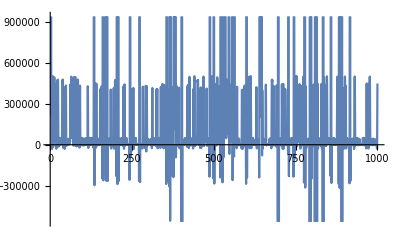

```mathematica
Plot[f[x],{x,1,1000}]
```

To calculate the value at missing cells we tried to generate a random value which is a real number by nature so that it derives a value very near to the real-life. Using this interpolation we obtained few values to be negative. As the property loss cannot be in negative we converted them into positive values in the next step.

```mathematica
calPropLoss[x_] := If[x==Quantity[0,"USDollars"], f[RandomReal[{1,61217}]],x]
```

```mathematica
TornadoData = TornadoData[All,{13->calPropLoss}]
```

Dataset[<>]

```mathematica
makePositive[x_] := If[x<Quantity[0,"USDollars"],x*(-1),x]
```

```mathematica
TornadoData = TornadoData[All,{13->makePositive}]
```

Dataset[<>]

Now considering the columns Start and End, we noticed that there are many cells with missing values. To get our training data in a functional manner we need to fill in these values with co-ordinates such that they look real. To bring this idea alive we filled all the missing values with the co-ordinates of Texas state as it is one of the states that is present in the center of U.S.

```mathematica
FillingCords = GeoPosition[TornadoData[18,1]]
```

GeoPosition[{32.7403,-89.6678}]

```mathematica
Cords[x_]:=If[x===Missing["NotAvailable"],FillingCords,x]
```

```mathematica
TornadoData = TornadoData[All,{10->Cords}]
```

Dataset[<>]

```mathematica
TornadoData = TornadoData[All,{11->Cords}]
```

Dataset[<>]

After reading the document on how the F-scale is calculated it was noticed that the scale calculation depends on the distance covered by the tornado. Utilizing the co-ordinates present in Start and End column we found the distance the tornado covered in miles and placed them in a new column called Distance. 

In the next step we performed a mathematical operation on the all the data in “Distance” which has its value more than 200 miles because of filling the co-ordinates of Texas in missing cells. The reason for using the value <25> is on examining the data it was noticed that no tornado covered more than that distance.

```mathematica
TornadoData = Append[#,"Distance"-> GeoDistance[#["Start"],#["End"]]]&/@TornadoData
```

Dataset[<>]

Step 15). We then remove units from “Fatalities”, “TotalLoss” and “Distance” columns by using the function RemoveUnits[] to atomise the data.

```mathematica
RemoveUnits[x_] := QuantityMagnitude[x]
```

```mathematica
TornadoData = TornadoData[All,{7->RemoveUnits}]
```

Dataset[<>]

```mathematica
TornadoData = TornadoData[All,{13->RemoveUnits}]
```

Dataset[<>]

```mathematica
TornadoData = TornadoData[All,{14->RemoveUnits}]
```

Dataset[<>]

Step 16). We then create a new column called “HumanDamage” by adding the values of columns “Injuries” and “Fatalities”.

```mathematica
TornadoData = Append[#,"HumanDamage"-> #["Injuries"]+#["Fatalities"]]&/@TornadoData
```

Dataset[<>]

```mathematica
DistanceChange[x_] := If[x>100,Mod[x,25],x]
```

```mathematica
TornadoData = TornadoData[All,{14->DistanceChange}]
```

Dataset[<>]

The purpose of performing this step is to utilize the update in the scaling of the tornado. After year <> the scaling of tornado has changed to EF-scale. So we decided to extract the Year in which the tornado occurred which can help the decision tree very well with the format and also simplicity in the data. The new column is named as “YearOccured”.

```mathematica
calcYear[x_]:=DateValue[x,"Year"]
TornadoData=Append[#,"YearOccured"->calcYear[#["Date"]]]&/@TornadoData
```

Dataset[<>]

# Feature Selection

The following columns TotalLoss, Distance, HumanDamage and Date as features to predict the magnitude of the Tornado.

```mathematica
Features = Map[{#TotalLoss,#Distance,#HumanDamage,#Date}->#Magnitude&,Normal[TornadoData]]
```

{{4500000,11.0595,3,Sat 31 Dec 1949 03:11:00CDT}→F3,{4500000,6.40594,3,Sat 31 Dec 1949 03:11:00CDT}→F3,61213,{10000.,0.774609,0,Mon 30 Nov 2015 04:08:30CDT}→EF1,{50000.,0.924498,0,Mon 30 Nov 2015 04:15:58CDT}→EF0}
 |  |  |  |

```mathematica
Features1=Map[{#TotalLoss,#Distance,#YearOccured,#HumanDamage,#Magnitude}&,Normal[TornadoData]]
```

{{4500000,11.0595,1949,3,F3},{4500000,6.40594,1949,3,F3},{450000,4.9051,1949,0,F3},{450000,4.00706,1949,3,F3},61210,{100000.,5.58162,2015,0,EF1},{10000.,0.774609,2015,0,EF1},{50000.,0.924498,2015,0,EF0}}
 |  |  |  |

Extracting the training data and testing data.

```mathematica
training = Drop[Features,{1,-1,5}]
testing = Take[Features,{1,-1,5}]
training1= Drop[Features1,{1,-1,5}]
testing1 = Take[Features1,{1,-1,5}]
```

{{4500000,6.40594,3,Sat 31 Dec 1949 03:11:00CDT}→F3,{450000,4.9051,0,Sat 31 Dec 1949 03:11:10CDT}→F3,48969,{100000.,5.58162,0,Mon 30 Nov 2015 04:05:43CDT}→EF1,{50000.,0.924498,0,Mon 30 Nov 2015 04:15:58CDT}→EF0}
 |  |  |  |

{{4500000,11.0595,3,Sat 31 Dec 1949 03:11:00CDT}→F3,{4500,19.3726,2,Sat 31 Dec 1949 13:05:25CDT}→F3,12240,{31989.3,24.3545,0,Mon 30 Nov 2015 03:23:10CDT}→EF1,{10000.,0.774609,0,Mon 30 Nov 2015 04:08:30CDT}→EF1}
 |  |  |  |

{{4500000,6.40594,1949,3,F3},{450000,4.9051,1949,0,F3},{450000,4.00706,1949,3,F3},{45000,2.88964,1949,1,F1},48966,{50000.,5.7353,2015,0,EF2},{100000.,5.58162,2015,0,EF1},{50000.,0.924498,2015,0,EF0}}
 |  |  |  |

{{4500000,11.0595,1949,3,F3},{4500,19.3726,1949,2,F3},{45000,11.4229,1950,13,F3},12238,{75000.,7.09325,2015,0,EF1},{31989.3,24.3545,2015,0,EF1},{10000.,0.774609,2015,0,EF1}}
 |  |  |  |

# Machine Learning algorithm application

## Neural Networks

```mathematica
classifier1 = Classify[training, Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[classifier1,testing,"Accuracy"]
```

0.555537

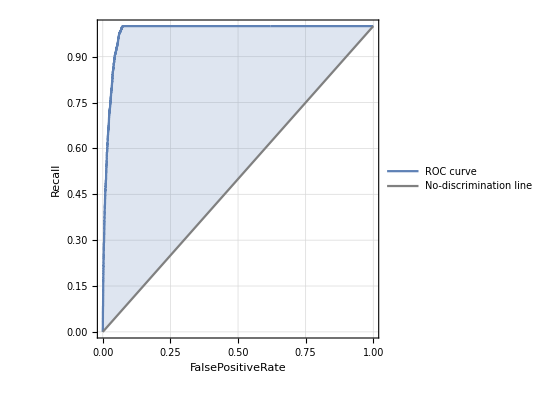
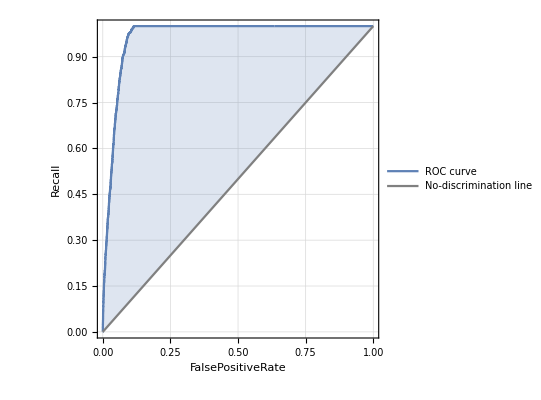
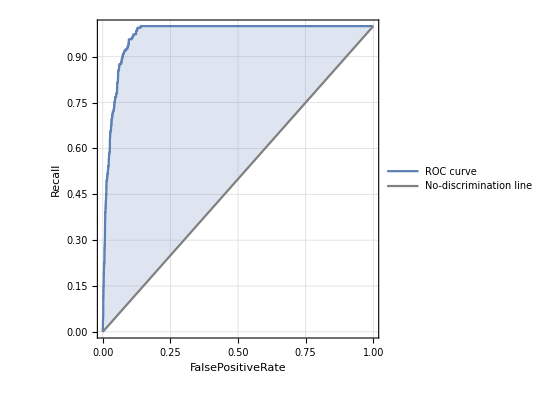
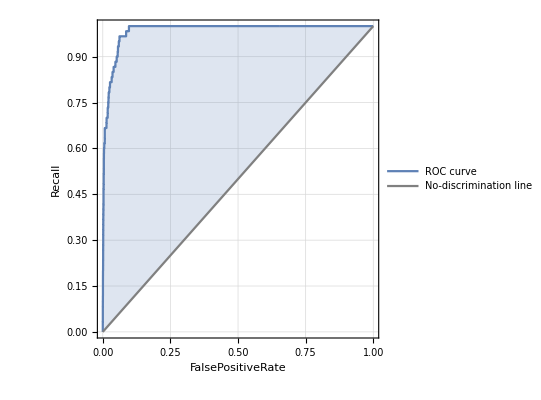
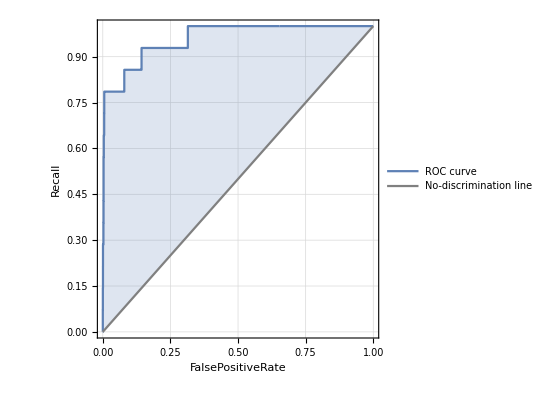
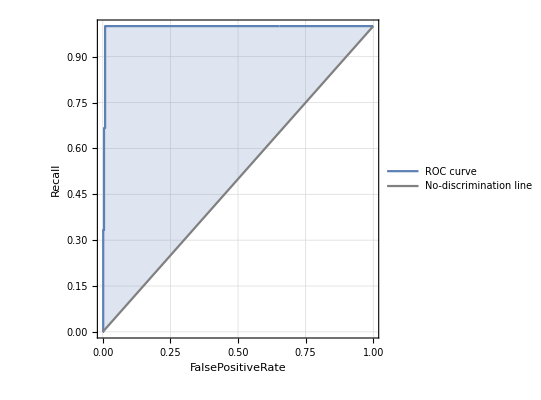
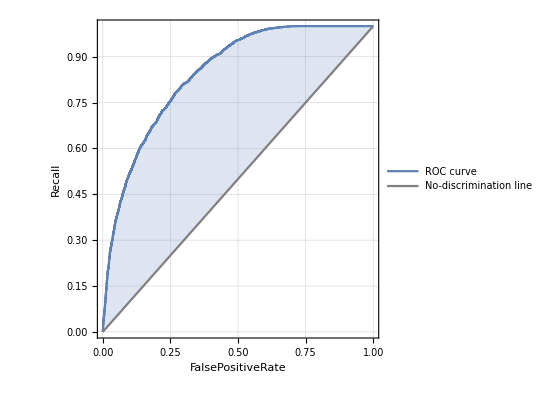
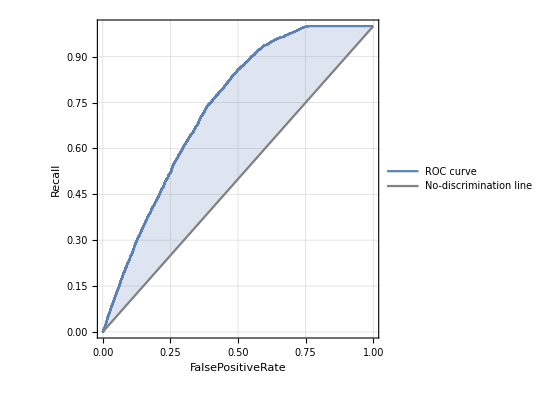
<|EF0→-Graphics-,EF1→-Graphics-,EF2→-Graphics-,EF3→-Graphics-,EF4→-Graphics-,EF5→-Graphics-,F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-,F5→-Graphics-|>

```mathematica
ClassifierMeasurements[classifier1,testing,"ROCCurve"]
```

```mathematica
ClassifierMeasurements[classifier1,testing,"Precision"]
```

<|EF0→0.698899,EF1→0.484401,EF2→0.390244,EF3→0.475,EF4→0.5,EF5→Indeterminate,F0→0.620653,F1→0.459406,F2→0.407742,F3→0.4,F4→0.530303,F5→Indeterminate|>

```mathematica
ClassifierMeasurements[classifier1,testing,"Recall"]
```

<|EF0→0.808182,EF1→0.459502,EF2→0.172043,EF3→0.316667,EF4→0.0714286,EF5→0.,F0→0.774922,F1→0.470875,F2→0.19713,F3→0.155738,F4→0.263158,F5→0.|>

## Decision Trees

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/AVCDecisionTreeForest.m"]
```

```mathematica
dtree=BuildDecisionTree[training1,{5,0},"ImpurityFunction"->"Gini"]
```

{{0.102447,50177/25,3,Number,48973},{1},{{0.0415388,0.973513,2,Number,7949},{1},{{0.0335091,0,4,Number,5210},{1},{{0.0480458,1663/100,4,Number,589},{1},{{0.0561375,1887/20,4,Number,104},{1},{1}}}}}}
 |  |  |  |

```mathematica
classResRules=DecisionTreeClassificationSuccess[dtree,testing1]
```

{{EF0,True}→0.707273,{EF0,False}→0.292727,{EF1,True}→0.386293,{EF1,False}→0.613707,{EF2,True}→0.295699,{EF2,False}→0.704301,{EF3,True}→0.183333,{EF3,False}→0.816667,{EF4,True}→0.357143,{EF4,False}→0.642857,{EF5,True}→0.,{EF5,False}→1.,{F0,True}→0.714222,{F0,False}→0.285778,{F1,True}→0.471449,{F1,False}→0.528551,{F2,True}→0.323144,{F2,False}→0.676856,{F3,True}→0.190574,{F3,False}→0.809426,{F4,True}→0.18797,{F4,False}→0.81203,{F5,True}→0.1875,{F5,False}→0.8125,{All,True}→0.539285,{All,False}→0.460715}

This image represents the graph plot of the decision tree formed. The image is attached here because it is taking alot of time to create the graph on evaluating the notebook. This image can be used to infer the decision tree formed.
-Graphics-
Accuracy Achieved = 0.544838
Precision, Recall and ROC curve can be interpreted from the following values:
{“EF0”,True}→0.700909,{“EF0”,False}→0.299091,{“EF1”,True}→0.429907,{“EF1”,False}→0.570093,{“EF2”,True}→0.258065,{“EF2”,False}→0.741935,{“EF3”,True}→0.2,{“EF3”,False}→0.8,{“EF4”,True}→0.357143,{“EF4”,False}→0.642857,{“EF5”,True}→0.,{“EF5”,False}→1.,{“F0”,True}→0.72397,{“F0”,False}→0.27603,{“F1”,True}→0.475466,{“F1”,False}→0.524534,{“F2”,True}→0.313163,{“F2”,False}→0.686837,{“F3”,True}→0.215164,{“F3”,False}→0.784836,{“F4”,True}→0.180451,{“F4”,False}→0.819549,{“F5”,True}→0.1875,{“F5”,False}→0.8125,{All,True}→0.544838,{All,False}→0.455162}

## Logistic Regression

```mathematica
classifier3 = Classify[training, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
testResults = Map[classifier3[Keys[#]]==Values[#]&,testing]
```

{False,False,False,False,False,False,False,True,False,True,False,True,True,False,True,True,False,True,False,True,True,True,False,False,True,False,False,True,12188,True,False,False,False,True,True,True,True,True,False,True,True,True,True,False,False,True,False,False,False,True,False,False,False,True,True,True,True}
 |  |  |  |

```mathematica
ClassifierMeasurements[classifier3,testing,"Accuracy"]
```

0.531526

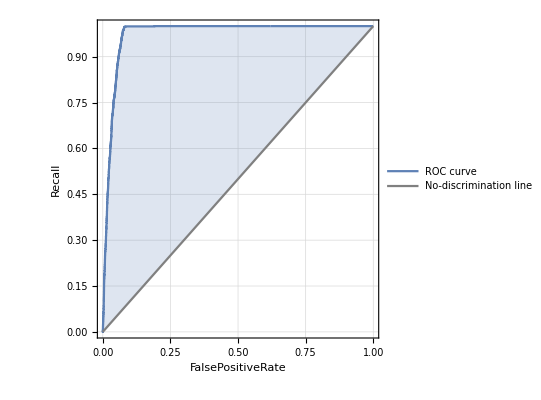
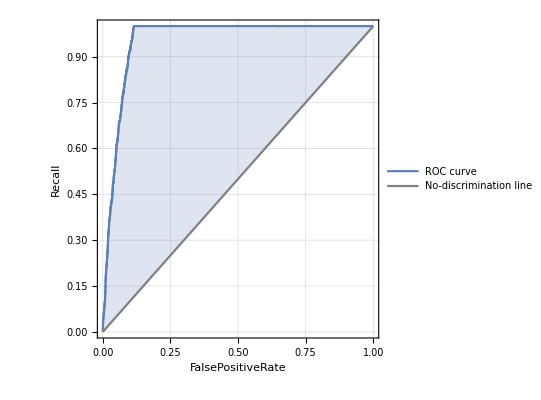
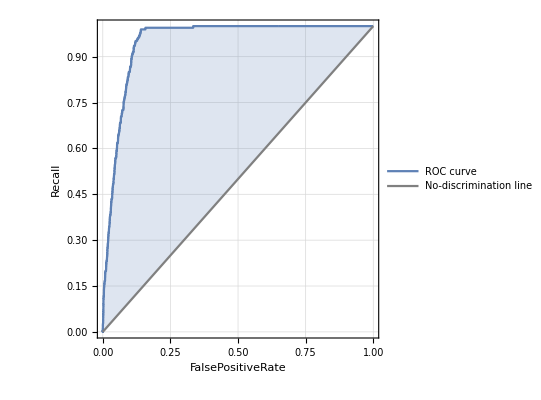
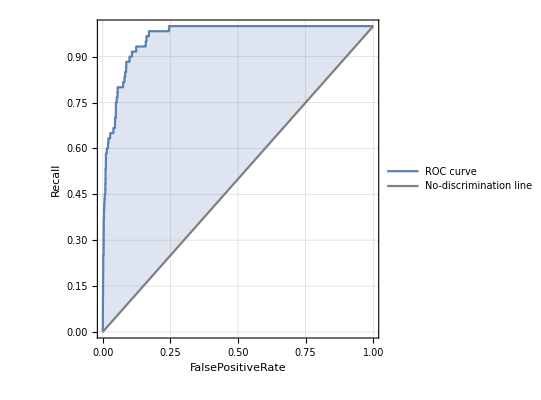
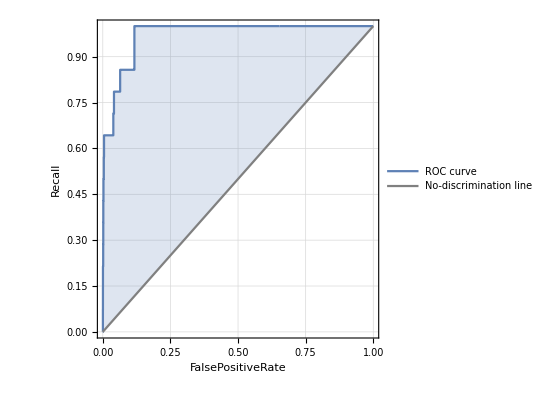
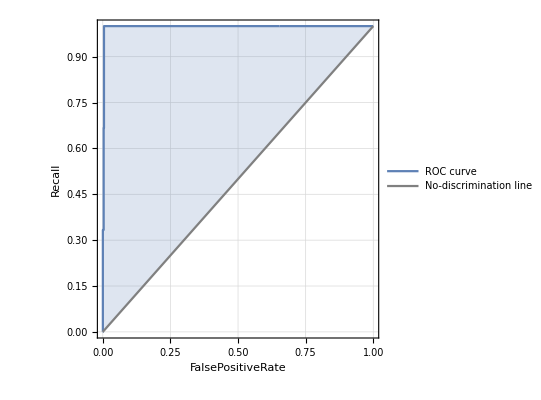
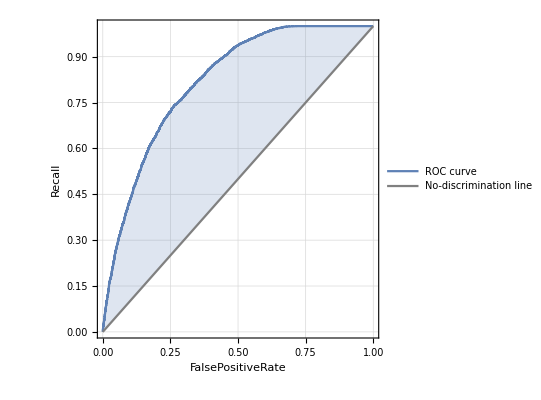
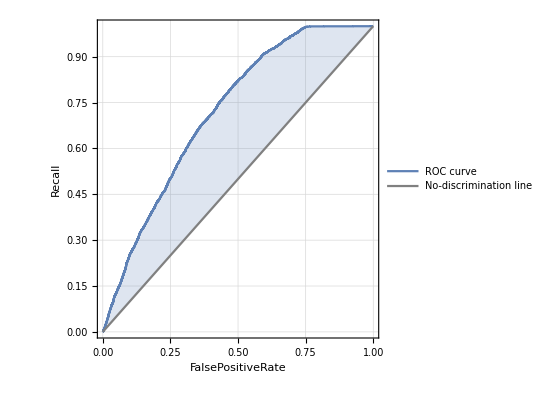
<|EF0→-Graphics-,EF1→-Graphics-,EF2→-Graphics-,EF3→-Graphics-,EF4→-Graphics-,EF5→-Graphics-,F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-,F5→-Graphics-|>

```mathematica
ClassifierMeasurements[classifier3,testing,"ROCCurve"]
```

```mathematica
ClassifierMeasurements[classifier3,testing,"Precision"]
```

<|EF0→0.59438,EF1→0.42953,EF2→0.384615,EF3→0.47619,EF4→0.25,EF5→Indeterminate,F0→0.601517,F1→0.441511,F2→0.361888,F3→0.415842,F4→0.487179,F5→0.|>

```mathematica
ClassifierMeasurements[classifier3,testing,"Recall"]
```

<|EF0→0.884545,EF1→0.199377,EF2→0.0537634,EF3→0.166667,EF4→0.214286,EF5→0.,F0→0.755428,F1→0.489527,F2→0.129133,F3→0.0860656,F4→0.142857,F5→0.|>

## Conclusions

After carefully observing the above algorithms It can be seen that the overall results achieved by the all the algorithms are very similar. But if we compare each class separately we can see that the classes with labels EF0 and F0 have higher success rates compared to the classes EF5 and F5. This occurs due to the amount of the data present with respect to each class in the given dataset available for training. From this evaluation we can conclude that Dataset consists of more tornadoes from classes EF0 and F0 compared to classes EF5 and F5 and thus the algorithms learned more about classes EF0 and F0 compared to EF5 and F5. The values of success had decreased consistently from EF0-EF5 and F0-F5 because there are large number of tornadoes from class EF0(F0) then EF1(F1) and so on till EF5(F5) in reality as well. Tornadoes with high severity of F5 and EF5 occurred very rarely.

So we can conclude that for an algorithm to learn/train uniformly there should be uniform distribution of all classes in the training data. Different proportions can sometimes cause over-fitting and under-fitting of the data.

## References

1.	Wolfram Research, “Tornadoes in the U.S., 1950-2015” from the Wolfram Data Repository. (2016) https://doi.org/10.24097/wolfram.33875.data
2.	Decision Tree adopted from the following link: https://github.com/antononcube/MathematicaForPrediction/blob/master/AVCDecisionTreeForest.m